```mathematica
(*  manca una lettera *)

ciphertext="
   KCCPKBGUFDPHQTYAVINRRTMVGRKDNBVFDETDGILTXRGUD
   DKOTFMBPVGEGLTGCKQRACQCWDNAWCRXIZAKFTLEWRPTYC QKYVXCHKFTPONCOQRHJVAJUWETMCMSPKQDYHJVDAHCTRL SVSKCGCZOODZXGSFRLSWCWSJTBHAFSIASPRJAHKJRJUMV GKMITZHFPDISPZLVLGWTFPLKKEBDPGCEBSHCTJRWXBAFS PEZQNRWXCVYCGAONWDDKACKAWBBIKFTIOVKCGGHJVLNHI FFSOESVYCLACNVRWBBIREPBBVFEXOSCDYGZWPFDTKFOIY CWHJVLNHIQIBTKHJVNPIST"
```

KCCPKBGUFDPHQTYAVINRRTMVGRKDNBVFDETDGILTXRGUD
   DKOTFMBPVGEGLTGCKQRACQCWDNAWCRXIZAKFTLEWRPTYC QKYVXCHKFTPONCOQRHJVAJUWETMCMSPKQDYHJVDAHCTRL SVSKCGCZOODZXGSFRLSWCWSJTBHAFSIASPRJAHKJRJUMV GKMITZHFPDISPZLVLGWTFPLKKEBDPGCEBSHCTJRWXBAFS PEZQNRWXCVYCGAONWDDKACKAWBBIKFTIOVKCGGHJVLNHI FFSOESVYCLACNVRWBBIREPBBVFEXOSCDYGZWPFDTKFOIY CWHJVLNHIQIBTKHJVNPIST

```mathematica
(* cifrato corretto *)

ciphertext="   KCCPKBGUFDPHQTYAVINRRTMVGRKDNBVFDETDGILTXRGUD
                DKOTFMBPVGEGLTGCKQRACQCWDNAWCRXIZAKFTLEWRPTYC
                QKYVXCHKFTPONCQQRHJVAJUWETMCMSPKQDYHJVDAHCTRL
                SVSKCGCZQQDZXGSFRLSWCWSJTBHAFSIASPRJAHKJRJUMV
                GKMITZHFPDISPZLVLGWTFPLKKEBDPGCEBSHCTJRWXBAFS
                PEZQNRWXCVYCGAONWDDKACKAWBBIKFTIOVKCGGHJVLNHI
                FFSQESVYCLACNVRWBBIREPBBVFEXOSCDYGZWPFDTKFQIY
                CWHJVLNHIQIBTKHJVNPIST"
```

KCCPKBGUFDPHQTYAVINRRTMVGRKDNBVFDETDGILTXRGUD
                DKOTFMBPVGEGLTGCKQRACQCWDNAWCRXIZAKFTLEWRPTYC
                QKYVXCHKFTPONCQQRHJVAJUWETMCMSPKQDYHJVDAHCTRL
                SVSKCGCZQQDZXGSFRLSWCWSJTBHAFSIASPRJAHKJRJUMV
                GKMITZHFPDISPZLVLGWTFPLKKEBDPGCEBSHCTJRWXBAFS
                PEZQNRWXCVYCGAONWDDKACKAWBBIKFTIOVKCGGHJVLNHI
                FFSQESVYCLACNVRWBBIREPBBVFEXOSCDYGZWPFDTKFQIY
                CWHJVLNHIQIBTKHJVNPIST

```mathematica
Test[x_]:=97<=x<=97+25
	ctx=Select[ToCharacterCode[ToLowerCase[ciphertext]],Test]-97
```

{10,2,2,15,10,1,6,20,5,3,15,7,16,19,24,0,21,8,13,17,17,19,12,21,6,17,10,3,13,1,21,5,3,4,19,3,6,8,11,19,23,17,6,20,3,3,10,14,19,5,12,1,15,21,6,4,6,11,19,6,2,10,16,17,0,2,16,2,22,3,13,0,22,2,17,23,8,25,0,10,5,19,11,4,22,17,15,19,24,2,16,10,24,21,23,2,7,10,5,19,15,14,13,2,16,16,17,7,9,21,0,9,20,22,4,19,12,2,12,18,15,10,16,3,24,7,9,21,3,0,7,2,19,17,11,18,21,18,10,2,6,2,25,16,16,3,25,23,6,18,5,17,11,18,22,2,22,18,9,19,1,7,0,5,18,8,0,18,15,17,9,0,7,10,9,17,9,20,12,21,6,10,12,8,19,25,7,5,15,3,8,18,15,25,11,21,11,6,22,19,5,15,11,10,10,4,1,3,15,6,2,4,1,18,7,2,19,9,17,22,23,1,0,5,18,15,4,25,16,13,17,22,23,2,21,24,2,6,0,14,13,22,3,3,10,0,2,10,0,22,1,1,8,10,5,19,8,14,21,10,2,6,6,7,9,21,11,13,7,8,5,5,18,16,4,18,21,24,2,11,0,2,13,21,17,22,1,1,8,17,4,15,1,1,21,5,4,23,14,18,2,3,24,6,25,22,15,5,3,19,10,5,16,8,24,2,22,7,9,21,11,13,7,8,16,8,1,19,10,7,9,21,13,15,8,18,19}

```mathematica
texteng=Import["http://www.nytimes.com"];
eng=Select[ToCharacterCode[ToLowerCase[texteng]],Test]-97;

TextDistribution[ctx_]:=
Module[{freqs,pY},(
freqs=Map[Count[ctx,#]&,Range[0,25]];
pY=freqs/Length[ctx];
N[pY]
)]
```

```mathematica
CoincidenceIndex[ctx_]:=N[Plus@@(TextDistribution[ctx]^2)]
```

```mathematica
peng=TextDistribution[eng]
```

{0.0785467,0.013581,0.0383914,0.0396261,0.127815,0.0149333,0.0165207,0.032571,0.0786642,0.00135223,0.0108178,0.0482686,0.0295138,0.0680228,0.0700218,0.0248692,0.000646716,0.0663766,0.083838,0.0809571,0.026339,0.010759,0.0182256,0.00117585,0.015286,0.00288083}

{14,14,24,16,10,15,16,14,14,11,20,11,6,10,11,15,7,16,15,19,4,18,14,7,8,7}

```mathematica
CoincidenceIndex[ctx]
```

0.0437179

```mathematica
pY=freqs/Length[ctx]
Abs[0.068-N[Plus@@(pY^2)]]
Abs[0.038-N[Plus@@(pY^2)]]
```

{14/337,14/337,24/337,16/337,10/337,15/337,16/337,14/337,14/337,11/337,20/337,11/337,6/337,10/337,11/337,15/337,7/337,16/337,15/337,19/337,4/337,18/337,14/337,7/337,8/337,7/337}

0.0247664

0.00523363

```mathematica
reps=Select[SortBy[Tally[partitioned=Partition[ctx,3,1]],Last],#[[2]]>=2&]
sequence=reps[[-1,1]]
positions=Flatten[Position[partitioned,sequence]]
distances=(Drop[positions,1]-Drop[positions,-1])
m=GCD@@distances
```

{{{0,5,18},2},{{1,1,8},2},{{1,21,5},2},{{3,3,10},2},{{7,2,19},2},{{9,21,11},2},{{10,2,6},2},{{11,13,7},2},{{12,21,6},2},{{13,7,8},2},{{17,11,18},2},{{17,22,23},2},{{21,11,13},2},{{21,24,2},2},{{22,1,1},2},{{10,5,19},3},{{7,9,21},5}}

{7,9,21}

{108,126,264,318,330}

{18,138,54,12}

6

```mathematica
monoblocks=Transpose[Partition[ctx,m]]
ics=Map[CoincidenceIndex,monoblocks]
```

{{10,6,16,13,6,21,6,6,19,6,2,16,22,0,22,16,7,13,9,4,15,9,19,10,16,5,22,0,15,9,6,7,15,22,10,2,19,0,16,21,13,2,8,21,9,5,21,13,8,21,2,15,16,9,16,9},{2,20,19,17,17,5,8,20,5,4,10,2,2,10,17,10,10,2,21,19,10,21,17,2,3,17,18,5,17,17,10,5,25,19,4,4,9,5,13,24,22,10,10,10,21,5,24,21,17,5,3,5,8,21,8,21},{2,5,24,17,10,3,11,3,12,6,16,22,17,5,15,24,5,16,0,12,16,3,11,6,25,11,9,18,9,9,12,15,11,5,1,1,17,18,17,2,3,0,5,2,11,18,2,17,4,4,24,3,24,11,1,13},{15,3,0,19,3,4,19,3,1,11,17,3,23,19,19,21,19,16,9,2,3,0,18,2,23,18,19,8,0,20,8,3,21,15,3,18,22,15,22,6,3,22,19,6,13,16,11,22,15,23,6,19,2,13,19,15},{10,15,21,12,13,19,23,10,15,19,0,13,8,11,24,23,15,17,20,12,24,7,21,25,6,22,1,0,7,12,19,8,11,11,15,7,23,4,23,0,10,1,8,6,7,4,0,1,1,14,25,10,22,7,10,8},{1,7,8,21,1,3,17,14,21,6,2,0,25,4,2,2,14,7,22,18,7,2,18,16,18,2,7,18,10,21,25,18,6,10,6,2,1,25,2,14,0,1,14,7,8,18,2,1,1,18,22,5,7,8,7,18}}

{0.0797194,0.100128,0.0663265,0.0816327,0.059949,0.0899235}

```mathematica
Abs[ics-0.068]
Abs[ics-0.038]
```

{0.0117194,0.0321276,0.00167347,0.0136327,0.00805102,0.0219235}

{0.0417194,0.0621276,0.0283265,0.0436327,0.021949,0.0519235}

4

{{22,2},{24,2},{25,2},{11,3},{1,4},{8,4},{10,4},{15,4},{19,4},{23,4},{0,5},{7,5}}

{18,20,21,7,23,4,6,11,15,19,22,3}

```mathematica
TextDistribution[Mod[monoblocks[[blk]]-keyguesses[[-4]],26]]
```

{0.0714286,0.,0.0178571,0.,0.0714286,0.0178571,0.0178571,0.0357143,0.0714286,0.0357143,0.0357143,0.0892857,0.0714286,0.,0.0357143,0.0357143,0.,0.0357143,0.0892857,0.0714286,0.,0.0714286,0.0535714,0.0357143,0.0178571,0.0178571}

# guessed -1
distance from english : 0.00106218
distance from random : 0.0310622

14

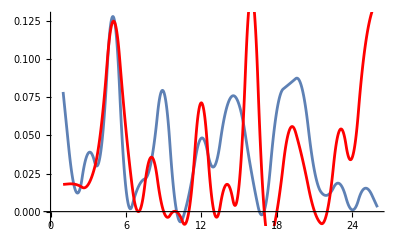

```mathematica
KeyGuess[blk=6]
G1=ListLinePlot[peng,InterpolationOrder->2];
G2=ListLinePlot[TextDistribution[Mod[monoblocks[[blk]]-keyguesses[[-3]],26]],InterpolationOrder->2,PlotStyle->Red];
Show[G1,G2]
```

```mathematica
MutualIncidence[block_]:=N[Plus@@(TextDistribution[block]peng)]

KeyGuess[blk_]:=(
mostfrequents=Take[SortBy[Tally[monoblocks[[blk]]],Last],-12];
keyguesses=Mod[Map[First,mostfrequents]-4,26];
mutualincidence=Map[MutualIncidence[Mod[monoblocks[[blk]]-#,26]]&,keyguesses];
keyguess=keyguesses[[pos=Position[mutualincidence,Max[mutualincidence]][[1,1]]]];
Print["# guessed ",pos-13,
   "\ndistance from english : ",Abs[Max@mutualincidence-0.068],
   "\ndistance from random : ",Abs[Max@mutualincidence-0.038]];
keyguess
)
```

```mathematica
key=Table[KeyGuess[i],{i,1,m}]
```

# guessed -3
distance from english : 0.00722335
distance from random : 0.0227766

# guessed -4
distance from english : 0.000864803
distance from random : 0.0308648

# guessed -6
distance from english : 0.011512
distance from random : 0.018488

# guessed -1
distance from english : 0.00443596
distance from random : 0.025564

# guessed -3
distance from english : 0.012921
distance from random : 0.017079

# guessed -1
distance from english : 0.00106218
distance from random : 0.0310622

{2,17,24,15,19,14}

```mathematica
key
FromCharacterCode[Flatten[Transpose[Mod[monoblocks-key,26]]]+97]
```

{2,17,24,15,19,14}

ilearnedhowtocalculatetheamountofpaperneededforaroomwheniwasatschoolyoumultiplythesquarefootageofthewallsbythecubiccontentsofthefloorandceilingcombinedanddoubleityouthenallowhalfthetotalforopeningssuchaswindowsanddoorsthenyouallowtheotherhalfformatchingthepatternthenyoudoublethewholethingagaintogiveamarginoferrorandthenyouorderthepape

```mathematica
k=y-4
```

```mathematica
N[1/26]
```

0.0384615

```mathematica
a
b
```

2

2

```mathematica
Apply[Plus,List[a,b]]
```

4

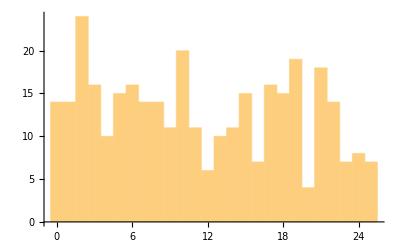

{{10,20},{2,24},{15,15},{1,14},{6,16},{20,4},{5,15},{3,16},{7,14},{14,11},{19,19},{24,8},{0,14},{21,18},{8,14},{13,10},{17,16},{12,6},{4,10},{11,11},{23,7},{16,7},{22,14},{25,7},{9,11},{18,15}}

```mathematica
Histogram[ctx,26]

Tally[ctx]
```